### Equilibrium & Eigenvalues

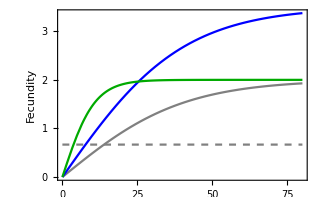
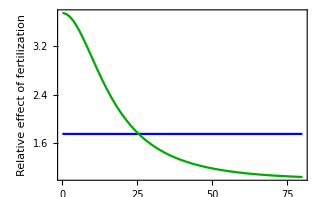
(a)

-Graphics-

(b)

-Graphics-
        Species ordered by competitiveness

```mathematica
Remove["Global`*"];
Clear["Global`*"];

q=0.3;
m=0.2;

frmopt[col_,fsize_]:={Frame->True,FrameStyle->Thickness[0.002],FrameTicksStyle->Directive[{col,FontFamily->"Times New Roman",FontSize->fsize}]};
fstylopt[txt_,fsize_]:=Style[txt,Black,FontFamily->"Times New Roman",FontSize->fsize]

ino=80;

f0[i_]:=2((1-Exp[-4 i/ino])/(1+Exp[-4 i/ino]));
f1[i_]:=3.5((1-Exp[-4 i/ino])/(1+Exp[-4 i/ino]));
f2[i_]:=2((1-Exp[-15 i/ino])/(1+Exp[-15 i/ino]));

g0=Plot[m/q,{i,0,ino},PlotStyle->{Gray,Dashed},Evaluate[frmopt[Black,12]],FrameLabel->{None,fstylopt["Fecundity",14]},ImageSize->320];
g1=Plot[{f0[i],f1[i],f2[i]},{i,0,ino},PlotStyle->{Gray,Blue,Darker[Green]},Evaluate[frmopt[Black,12]],FrameLabel->{None,fstylopt["Fecundity",14]},ImageSize->320];
g2=Plot[{f1[i]/f0[i],f2[i]/f0[i]},{i,0,ino},PlotStyle->{Blue,Darker[Green]},PlotRange->{0,All},Evaluate[frmopt[Black,12]],FrameLabel->{None,fstylopt["Relative effect of fertilization",14]},ImageSize->320];

g3=Column[{
fstylopt["(a)",16],Spacer[{0,0}],Show[g1,g0],Spacer[{0,0}],
fstylopt["(b)",16],Spacer[{0,0}],g2,
Item[Style["        Species ordered by competitiveness",Black,FontFamily->"Times New Roman",FontSize->14],Alignment->Center]
},Alignment->Left];

Print[g3];
```

```mathematica
(* Figure export *)

figfile=0;  (* If figfile=1, plots are output as files *)

If[figfile==1,
Export[StringJoin[NotebookDirectory[],"Fig_tradeoff.pdf"],g3];
Print["Figure is exported ..."];
,
Print["Files is not exported ..."];
]
```

Figure is exported ...

```mathematica
numeriana[ftype_]:=Do[

q=0.3;
m=0.2;
η = m/q;

Switch[ftype,
1,f[i_]:=f1[i],
2,f[i_]:=f2[i],
_,f[i_]:=f0[i]
];

For[i=1,i≤ino,i++,
Subscript[d0, i]=(q f[i](1-∑_(j=1)^i Subscript[pn, j])-q ∑_(j=1)^(i-1) Subscript[pn, j] f[j]-m)Subscript[pn, i];
];

Subscript[sp, 0]=0;
Subscript[spf, 0]=0;
For[i=1,i≤ino,i++,
If[f[i]≤η ,Subscript[pp, i]=0,Subscript[pp, i]=1-Subscript[sp, i-1]-1/f[i](η+Subscript[spf, i-1])];
If[Subscript[pp, i]<0,Subscript[pp, i]=0];
Subscript[sp, i]=Subscript[sp, i-1]+Subscript[pp, i];
Subscript[spf, i]=Subscript[spf, i-1]+Subscript[pp, i] f[i];
];
];
```

```mathematica
numeriana[0];
inita=Table[{i,Subscript[pp, i]},{i,1,ino}];

inifredis=Graphics[{EdgeForm[{Thin,GrayLevel[0.7]}],GrayLevel[0.7],Rectangle[{(#1-0.4),0},{(#1+0.4),#2}]&@@@inita},frmopt[Black,12],PlotRangePadding->None,AspectRatio->0.8,ImageSize->{Automatic,240}];

numeriana[1];
endta1=Table[{i,Subscript[pp, i]},{i,1,ino}];

endfredis[1]=Graphics[{EdgeForm[{Thin,GrayLevel[0.7]}],GrayLevel[0.7],Rectangle[{(#1-0.4),0},{(#1+0.4),#2}]&@@@endta1},frmopt[Black,12],PlotRangePadding->None,AspectRatio->0.8,ImageSize->{Automatic,240}];

numeriana[2];
endta2=Table[{i,Subscript[pp, i]},{i,1,ino}];

endfredis[2]=Graphics[{EdgeForm[{Thin,GrayLevel[0.7]}],GrayLevel[0.7],Rectangle[{(#1-0.4),0},{(#1+0.4),#2}]&@@@endta2},frmopt[Black,12],PlotRangePadding->None,AspectRatio->0.8,ImageSize->{Automatic,240}];
```

### Simulation

#### NDSovle with Default precision q = 0.3, m =0. 2, n = 80, tmax = 500,000 (if error occurs during calculation, try to decrease “tmin0”)

```mathematica
calc[q_,m_,tminc_,tmaxc_,tc_]:=Do[
pinit=Table[inita[[i]][[2]],{i,1,ino}];
tpinit=Total[pinit];
If[tpinit>1,pinit=pinit/tpinit];

pinit=Table[inita[[i]][[2]],{i,1,ino}];

immig=10^-10;

f[i_]:=f0[i];
ps0=NDSolveValue[
Join[Table[Subscript[p, i]'[t]==(q f[i](1-∑_(j=1)^i Subscript[p, j][t])-q ∑_(j=1)^(i-1) Subscript[p, j][t]f[j]-m)Subscript[p, i][t]+immig,{i,1,ino}],
Table[Subscript[p, i][0]==pinit[[i]],{i,1,ino}]],Table[Subscript[p, i],{i,1,ino}],{t,tminc,tc}
];

f[i_]:=f1[i];
ps1=NDSolveValue[
Join[Table[Subscript[p, i]'[t]==(q f[i](1-∑_(j=1)^i Subscript[p, j][t])-q ∑_(j=1)^(i-1) Subscript[p, j][t]f[j]-m)Subscript[p, i][t]+immig,{i,1,ino}],
Table[Subscript[p, i][tc]==ps0[[i]][tc],{i,1,ino}]],Table[Subscript[p, i],{i,1,ino}],{t,tc,tmaxc}
];

f[i_]:=f2[i];
ps2=NDSolveValue[
Join[Table[Subscript[p, i]'[t]==(q f[i](1-∑_(j=1)^i Subscript[p, j][t])-q ∑_(j=1)^(i-1) Subscript[p, j][t]f[j]-m)Subscript[p, i][t]+immig,{i,1,ino}],
Table[Subscript[p, i][tc]==ps0[[i]][tc],{i,1,ino}]],Table[Subscript[p, i],{i,1,ino}],{t,tc,tmaxc}
];

Print["NDSolve finished!"];
];
```

```mathematica
pscale=0.04;

psampleno=400;
frameopt={FrameStyle->Thickness[0.002],FrameTicksStyle->Directive[{Black,FontFamily->"Times New Roman",FontSize->12}]};

gdraw[tmin_,tmax_,tc_]:=Do[

If[j==1,
dta0=Table[Table[N[If[τ<tc,ps0[[i]][τ],ps1[[i]][τ]],$MachinePrecision],{i,1,ino}],{τ,tmin,tmax,(tmax-tmin)/psampleno}],
dta0=Table[Table[N[If[τ<tc,ps0[[i]][τ],ps2[[i]][τ]],$MachinePrecision],{i,1,ino}],{τ,tmin,tmax,(tmax-tmin)/psampleno}]
];
Print["Type ",j,": Data extraction finished!"];

plt1=ListPlot[Table[Table[{∑_(j=1)^i dta0[[τ]][[j]],tmin+(τ-1)(tmax-tmin)/psampleno},{τ,1,psampleno+1}],{i,1,ino}],Joined->True,PlotRange->{{0.00000001,0.75},Automatic},Frame->True,Evaluate[frameopt],AspectRatio->1.2,ImageSize->{Automatic,250},PlotRangePadding->None];
plt2=ListPlot[Table[Table[{tmin+(τ-1)(tmax-tmin)/psampleno,∑_(j=1)^i dta0[[τ]][[j]]},{τ,1,psampleno+1}],{i,ino,ino}],Joined->True,PlotRange->{Automatic,{0.00000001,0.75}},Frame->True,Evaluate[frameopt],AspectRatio->1.2,ImageSize->{Automatic,250},PlotRangePadding->None,Filling->Top];
(* change a direction of plot *);
ref1=MapAt[GeometricTransformation[#,ReflectionTransform[{-1,1}]]&,plt2,{1}];
ref2=Graphics[ref1[[1]],PlotRange->Reverse@PlotRange[ref1],ref1[[2]]];

ref1s[j]=Show[plt1,ref2];

dta1=dta0/.x_/;x>pscale->pscale; (*if x is greater than 'pscale', it is replaced by 'pscale' *)
apta[j]=ArrayPlot[dta1,ColorFunction->(ColorData[{"LakeColors","Reverse"}][Rescale[#,{-0.001,pscale}]]&),ColorFunctionScaling->False,PlotRange->{-0.001,pscale},PlotRangePadding->None,ClippingStyle->Automatic,AspectRatio->1,FrameTicks->{{(*newtickv*) None,None},{(*newtickh*)Automatic,None}},DataReversed->True,PlotLegends->True,Evaluate[frameopt],ImageSize->{Automatic,242}];
leg0=apta[j][[2]][[1]];
leg1[j]=Append[leg0//.{360->160, {}->Directive[{Black,FontFamily->"Times New Roman",FontSize->11}]},TicksStyle->Thickness[0.002]];

,{j,1,2}
];

RADdraw[ri_,minlog_]:=Do[
(* --- rank-abundance curves *)

grayco=0.5;
sptopno=8;

total=Sum[p[i],{i,1,ino}];
tas=Sort[Table[{i,p[i]/total},{i,1,ino}],#1[[2]]>#2[[2]]&];
tas2=Split[tas,#2[[2]]>10^minlog&][[1]];
	(* tas2 ... (competitiveness, frequency) in rank order *)
tahist[ri]=tas2;
tas3=Table[{i,Log[10,tas2[[i]][[2]]]},{i,1,Length[tas2]}];

spinita=Table[If[inita[[tas2[[i]][[1]]]][[2]]≠0,tas3[[i]],Nothing],{i,1,Length[tas2]}];
spnonta=Table[If[inita[[tas2[[i]][[1]]]][[2]]==0,tas3[[i]],Nothing],{i,1,Length[tas2]}];

spexist=0;
For[i=1,i≤sptopno,i++,
sptopg=Select[tas2,MemberQ[#,tahist[0][[i]][[1]]]&];
If[UnsameQ[sptopg,{}],
spexist++;
sptopposi=Position[tas2,sptopg[[1]][[1]]];
sptop[spexist]=If[UnsameQ[sptopposi,{}],sptopposi[[1]][[1]],0];
];
];
spinitop=Table[If[sptop[i]≠0,{sptop[i],Log[10,tas2[[sptop[i]]][[2]]]},Nothing],{i,1,spexist}];

For[i=1,i≤Length[spinitop],i++,
po=Position[spinita,spinitop[[i]]][[1]][[1]];
spinita=Delete[spinita,po];
];

Print["Number of detectable species : ",Length[tas2],"    Number of non-origina species : ",Length[spnonta]];

frtick={FrameTicks->{{{#,PaddedForm[#,{2,1}]}& /@{-7.0,-6.0,-5.0,-4.0,-3.0,-2.0,-1.0,0.0},Automatic},Automatic},FrameTicksStyle->Directive[{Black,FontFamily->"Times New Roman",FontSize->12}]};

gts1=ListPlot[tas3,PlotRange->{{0,ino},{minlog-1,All}},Joined->True,PlotStyle->Gray,Mesh->None,PlotStyle->{GrayLevel[grayco]},Frame->True,PlotRangePadding->Scaled[.02],frtick,ImageSize->280];
gts2=ListPlot[spinita,PlotRange->{{0,ino},{minlog-1,All}},Joined->False,PlotMarkers->Graphics[{GrayLevel[grayco],Thickness[0.1],Circle[]},ImageSize->9],Frame->True,PlotRangePadding->Scaled[.02],frtick,ImageSize->280];
gts3=ListPlot[spnonta,PlotRange->{{0,ino},{minlog-1,All}},Joined->False,PlotMarkers->Graphics[{Red,Thickness[0.15],Circle[]},ImageSize->9],Frame->True,PlotRangePadding->Scaled[.02],frtick,ImageSize->280];
gts4=ListPlot[spinitop,PlotRange->{{0,ino},{minlog-1,All}},Joined->False,PlotMarkers->Graphics[{Lighter[Blue],Disk[]},ImageSize->8],Frame->True,PlotRangePadding->Scaled[.02],frtick,ImageSize->280];

gtts[ri]=Show[gts1,gts2,gts3,gts4,FrameTicks->{{Automatic,None},{None,None}}];
];
```

```mathematica
Graphics`PlotMarkers[]
```

{{●,10.96},{■,8.96},{◆,10.88},{▲,10.24},{▼,10.24},{○,10.24},{□,10.24},{◇,10.24},{△,11.136},{▽,11.136}}

```mathematica
(* Main *)

tmax0=100000; (* min time range for NDSolve *)
tmin0=0; (* max time range for NDSolve *)
tmaxr0=50000; (* max time for determination of p *)
tminr0=0; (* min time for determination of p *)

tchange=10000;

ctime=Timing[
calc[q,m,tmin0,tmax0,tchange];
gdraw[tminr0,tmaxr0,tchange];
];
Print["    --- Time for calculation : ",Style[ctime[[1]],FontColor->Blue]," sec"];
```

NDSolve finished!

Type 1: Data extraction finished!

Type 2: Data extraction finished!

--- Time for calculation : 62.5176 sec

```mathematica
minlogs=-5;
gmax=-0.0;

Print["Equilibria"];
Print["-- With origical fecundity"];
For[i=1,i≤ino,i++,p[i]=inita[[i]][[2]]];
RADdraw[0,minlogs];
Print[" -- With fertilized fecundity type 1"];
For[i=1,i≤ino,i++,p[i]=endta1[[i]][[2]]];
RADdraw[20,minlogs];
Print[" -- With fertilized fecundity type 2"];
For[i=1,i≤ino,i++,p[i]=endta2[[i]][[2]]];
RADdraw[21,minlogs];
```

Equilibria

-- With origical fecundity

Number of detectable species : 48    Number of non-origina species : 0

-- With fertilized fecundity type 1

Number of detectable species : 48    Number of non-origina species : 7

-- With fertilized fecundity type 2

Number of detectable species : 35    Number of non-origina species : 12

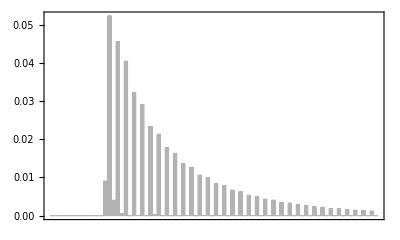
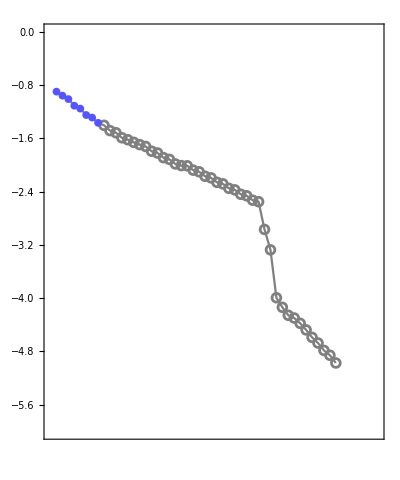
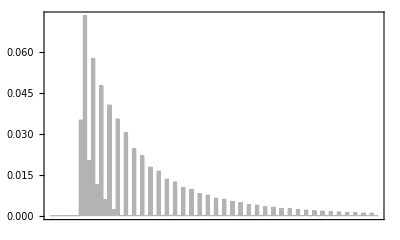
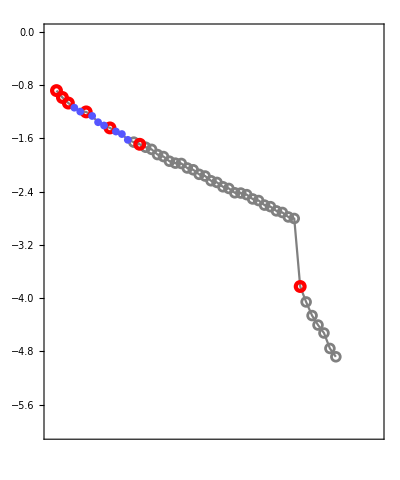
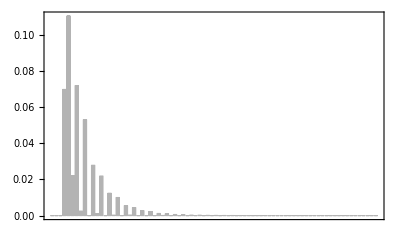
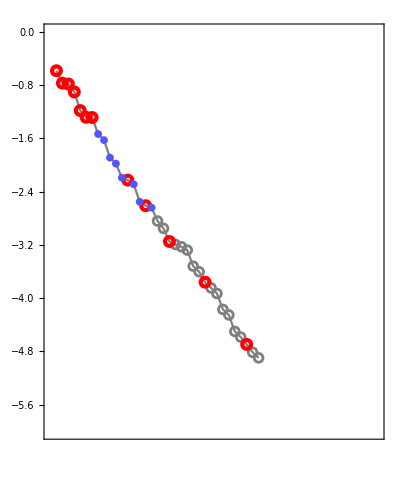
|  |  |  | 
 | (a)  Original  (f_(0,i)) |  |  | 
 |  |  |  | 
  Equilibrium frequency | -Graphics- |  | Log_10[Relative abundance] | -Graphics-
 |  |  |  | 
 | (b)  Fertilization type 1  (f_(3,i)) |  |  | 
 |  |  |  | 
  Equilibrium frequency | -Graphics- |  | Log_10[Relative abundance] | -Graphics-
 |  |  |  | 
 | (c)  Fertilization type 2  (f_(4,i)) |  |  | 
 |  |  |  | 
  Equilibrium frequency | -Graphics- |  | Log_10[Relative abundance] | -Graphics-
 |        Species ordered by competitiveness |  |  | Rank

```mathematica
gt1=Grid[{
{Spacer[{0,0}]},{"",Item[fstylopt["(a)  Original  (f_(0,i))",14],Alignment->Left]},{Spacer[{0,0}]},
{Item[Rotate[fstylopt["  Equilibrium frequency",14],Pi/2]],
Show[inifredis,FrameTicks->{{Automatic,None},{None,None}},AspectRatio->0.6,ImageSize->{Automatic,150}],Spacer[{5,0}],
Item[Rotate[fstylopt["Log_10[Relative abundance]",14],Pi/2]],
Show[gtts[0],PlotRange->{{0,55},{minlogs-1,0}},Axes->None,AspectRatio->1.2,ImageSize->{Automatic,150}]},

{Spacer[{0,0}]},{"",Item[fstylopt["(b)  Fertilization type 1  (f_(3,i))",14],Alignment->Left]},{Spacer[{0,0}]},
{Item[Rotate[fstylopt["  Equilibrium frequency",14],Pi/2]],
Show[endfredis[1],FrameTicks->{{Automatic,None},{None,None}},AspectRatio->0.6,ImageSize->{Automatic,150}],Spacer[{5,0}],
Item[Rotate[fstylopt["Log_10[Relative abundance]",14],Pi/2]],Show[gtts[20],PlotRange->{{0,55},{minlogs-1,0}},Axes->None,AspectRatio->1.2,ImageSize->{Automatic,150}]},

{Spacer[{0,0}]},{"",Item[fstylopt["(c)  Fertilization type 2  (f_(4,i))",14],Alignment->Left]},{Spacer[{0,0}]},
{Item[Rotate[fstylopt["  Equilibrium frequency",14],Pi/2]],
Show[endfredis[2],FrameTicks->{{Automatic,None},{None,None}},AspectRatio->0.6,ImageSize->{Automatic,150}],Spacer[{5,0}],
Item[Rotate[fstylopt["Log_10[Relative abundance]",14],Pi/2]],
Show[gtts[21],PlotRange->{{0,55},{minlogs-1,0}},Axes->None,AspectRatio->1.2,ImageSize->{Automatic,150}]},
{"",Item[fstylopt["       Species ordered by competitiveness",14]],Spacer[{0,0}],"",
Item[fstylopt["Rank ",14]]
}
},Alignment->Bottom]
```

```mathematica
(* Figure export *)

figfile=0;  (* If figfile=1, plots are output as files *)

If[figfile==1,
Export[StringJoin[NotebookDirectory[],"Fig_equil.pdf"],gt1];
Print["Figure is exported ..."];
,
Print["Files is not exported ..."];
]
```

Figure is exported ...

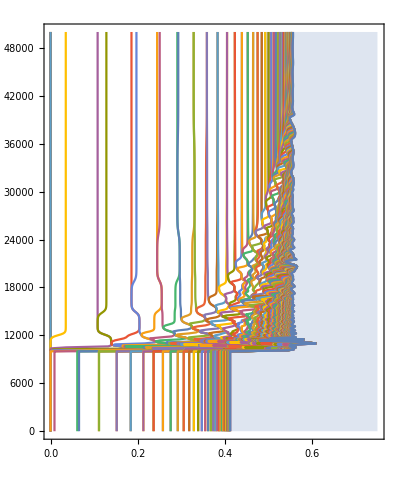
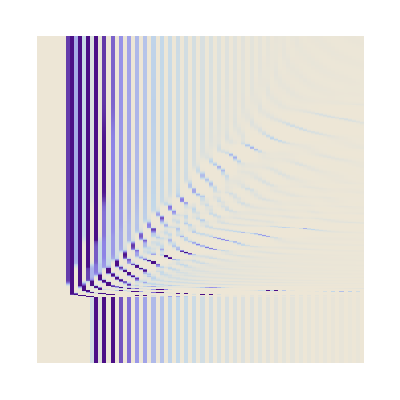
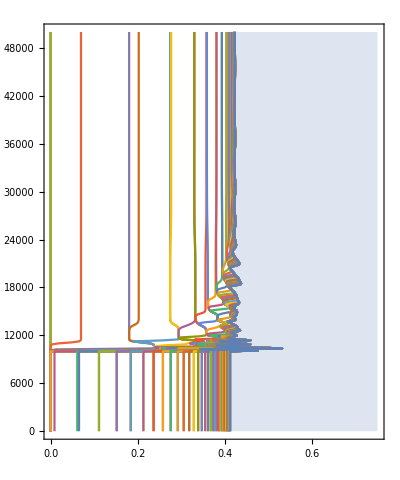
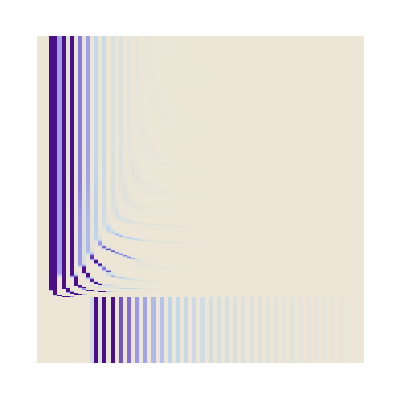
|  |  | 
 | (a)  Fertilization type 1  (f_(0,i) → f_(3,i)) |  | 
 |  |  | 
Time | -Graphics- | -Graphics- | 
 |  |  | 
 | (b)  Fertilization type 2  (f_(0,i) → f_(4,i)) |  | 
 |  |  | 
Time | -Graphics- | -Graphics- | 
 | Cumulative frequencies          | Species ordered by competitiveness |

```mathematica
gt2=Grid[{
{Spacer[{0,0}]},
{"",Item[fstylopt["(a)  Fertilization type 1  (f_(0,i) → f_(3,i))",15],Alignment->Left]},{Spacer[{0,0}]},
{Item[Rotate[fstylopt["Time",14],Pi/2],Alignment->Center],ref1s[1],apta[1][[1]],""},
{Spacer[{0,0}]},
{"",Item[fstylopt["(b)  Fertilization type 2  (f_(0,i) → f_(4,i))",15],Alignment->Left]},
{Spacer[{0,0}]},
{Item[Rotate[fstylopt["Time",14],Pi/2],Alignment->Center],ref1s[2],apta[2][[1]],leg1[2]},
{"",
Item[fstylopt["Cumulative frequencies"<>StringRepeat[" ",9],14],Alignment->Right],fstylopt["Species ordered by competitiveness",14]}
},Alignment->Bottom];

Print[gt2]
```

```mathematica
(* Figure export *)

figfile=0;  (* If figfile=1, plots are output as files *)

If[figfile==1,
Export[StringJoin[NotebookDirectory[],"Fig_freq.pdf"],gt2];
Print["Figure is exported ..."];
,
Print["Files is not exported ..."];
]
```

Files is not exported ...

Number of detectable species : 49    Number of non-origina species : 0

Number of detectable species : 60    Number of non-origina species : 20

Number of detectable species : 69    Number of non-origina species : 22

Number of detectable species : 72    Number of non-origina species : 23

Number of detectable species : 67    Number of non-origina species : 19

Number of detectable species : 65    Number of non-origina species : 17

Number of detectable species : 64    Number of non-origina species : 16

Number of detectable species : 63    Number of non-origina species : 16

Number of detectable species : 63    Number of non-origina species : 15

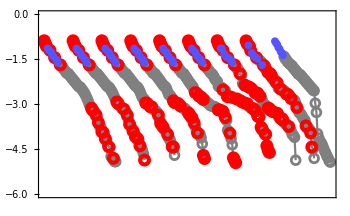

```mathematica
minlogs=-5;

ttno=9;
tinterval=10000;
For[ti=1,ti≤ttno,ti++,
For[i=1,i≤ino,i++,p[i]=ps1[[i]][tchange+(ti-1)tinterval]];
RADdraw[ti,minlogs];
];

shiftlen=-25;
grad1=Show[gtts[1],Table[Graphics[Translate[gtts[ttype][[1]],{(ttype-1)*shiftlen,0}]],{ttype,2,ttno}],PlotRange->{minlogs-1,gmax},Axes->None,ImageSize->350]
```

Number of detectable species : 49    Number of non-origina species : 0

Number of detectable species : 19    Number of non-origina species : 10

Number of detectable species : 61    Number of non-origina species : 22

Number of detectable species : 45    Number of non-origina species : 18

Number of detectable species : 45    Number of non-origina species : 18

Number of detectable species : 47    Number of non-origina species : 18

Number of detectable species : 54    Number of non-origina species : 20

Number of detectable species : 45    Number of non-origina species : 18

Number of detectable species : 49    Number of non-origina species : 19

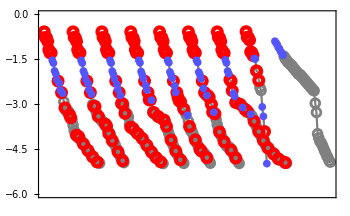

```mathematica
minlogs=-5;

ttno=9;
tinterval=10000;
For[ti=1,ti≤ttno,ti++,
For[i=1,i≤ino,i++,p[i]=ps2[[i]][tchange+(ti-1)tinterval]];
RADdraw[ti,minlogs];
];

shiftlen=-25;
grad2=Show[gtts[1],Table[Graphics[Translate[gtts[ttype][[1]],{(ttype-1)*shiftlen,0}]],{ttype,2,ttno}],PlotRange->{minlogs-1,gmax},Axes->None,ImageSize->350]
```

```mathematica
gt3=Grid[{
{Spacer[{0,0}]},
{"",Item[fstylopt["(a)  Fertilization type 1  (f_(0,i) → f_(3,i))",15],Alignment->Left]},{Spacer[{0,0}]},
{Item[Rotate[fstylopt["Log_10[Relative abundance]",14],Pi/2],Alignment->Center],grad1},
{Spacer[{0,0}]},
{"",Item[fstylopt["(b)  Fertilization type 2  (f_(0,i) → f_(4,i))",15],Alignment->Left]},
{Spacer[{0,0}]},
{Item[Rotate[fstylopt["Log_10[Relative abundance]",14],Pi/2],Alignment->Center],grad2}
},Alignment->Bottom]
```

| 
 | (a)  Fertilization type 1  (f_(0,i) → f_(3,i))
 | 
Log_10[Relative abundance] | -Graphics-
 | 
 | (b)  Fertilization type 2  (f_(0,i) → f_(4,i))
 | 
Log_10[Relative abundance] | -Graphics-

```mathematica
(* Figure export *)

figfile=0;  (* If figfile=1, plots are output as files *)

If[figfile==1,
Export[StringJoin[NotebookDirectory[],"Fig_temp_change.pdf"],gt3];
Print["Figure is exported ..."];
,
Print["Files is not exported ..."];
]
```

Files is not exported ...

### Initial frequency

```mathematica
inita
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0.00904409},{15,0.0522965},{16,0.00401709},{17,0.0455568},{18,0.000443707},{19,0.0404316},{20,0},{21,0.0321276},{22,0.000020698},{23,0.0290703},{24,0},{25,0.0232806},{26,0.000219259},{27,0.0213179},{28,0},{29,0.0177652},{30,0},{31,0.0163046},{32,0},{33,0.0135731},{34,0.0000417535},{35,0.0126234},{36,0},{37,0.0105963},{38,0.0000299897},{39,0.00990213},{40,0},{41,0.00836115},{42,0.0000227546},{43,0.00784196},{44,0},{45,0.00665121},{46,0.0000172137},{47,0.00625583},{48,0},{49,0.00532285},{50,0.0000137179},{51,0.00501748},{52,0},{53,0.00428029},{54,0.0000105969},{55,0.00404178},{56,0},{57,0.00345403},{58,8.71915×10^-6},{59,0.00326606},{60,0},{61,0.0027957},{62,6.75167×10^-6},{63,0.0026465},{64,0},{65,0.0022675},{66,5.70478×10^-6},{67,0.00214838},{68,0},{69,0.00184285},{70,4.36937×10^-6},{71,0.00174731},{72,0},{73,0.00149941},{74,3.79946×10^-6},{75,0.00142249},{76,0},{77,0.00122184},{78,2.84151×10^-6},{79,0.00115971},{80,0}}

```mathematica
tahist[0]
```

{{15,0.126932},{17,0.110574},{19,0.0981342},{21,0.0779791},{23,0.0705583},{25,0.0565057},{27,0.051742},{29,0.0431191},{31,0.0395739},{33,0.0329442},{35,0.0306391},{37,0.0257189},{39,0.0240341},{14,0.0219515},{41,0.0202939},{43,0.0190337},{45,0.0161436},{47,0.0151839},{49,0.0129194},{51,0.0121782},{53,0.010389},{55,0.00981006},{16,0.00975013},{57,0.00838349},{59,0.00792726},{61,0.00678563},{63,0.0064235},{65,0.00550359},{67,0.00521448},{69,0.0044729},{71,0.004241},{73,0.00363933},{75,0.00345261},{77,0.0029656},{79,0.00281481},{18,0.00107695},{26,0.000532176},{34,0.000101343},{38,0.00007279},{42,0.0000552292},{22,0.0000502374},{46,0.0000417804},{50,0.0000332957},{54,0.0000257203},{58,0.0000211628},{62,0.0000163874},{66,0.0000138464},{70,0.0000106052}}

### Final frequencies type 1

```mathematica
endta1
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0.0349544},{9,0.0730686},{10,0.0200802},{11,0.0575648},{12,0.0113981},{13,0.0474901},{14,0.00587077},{15,0.0404686},{16,0.00212779},{17,0.0353225},{18,0},{19,0.0303762},{20,0},{21,0.0244656},{22,0},{23,0.021833},{24,0},{25,0.0177359},{26,0.0000303849},{27,0.0162483},{28,0},{29,0.0132993},{30,0.0000830929},{31,0.0122878},{32,0},{33,0.0102969},{34,0},{35,0.00956909},{36,0},{37,0.0079838},{38,0.0000486854},{39,0.00745948},{40,0},{41,0.00634591},{42,0},{43,0.00593701},{44,0},{45,0.0050189},{46,0.0000219054},{47,0.00472011},{48,0},{49,0.00403247},{50,1.63817×10^-6},{51,0.00380156},{52,0},{53,0.00322697},{54,0.0000166124},{55,0.00304672},{56,0},{57,0.00261952},{58,0},{59,0.00247358},{60,0},{61,0.0021087},{62,9.74191×10^-6},{63,0.00199594},{64,0},{65,0.00171868},{66,0},{67,0.00162804},{68,0},{69,0.00138906},{70,7.30056×10^-6},{71,0.00131685},{72,0},{73,0.00113743},{74,0},{75,0.00107707},{76,0},{77,0.000921861},{78,3.90852×10^-6},{79,0.0008749},{80,0}}

```mathematica
tahist[20]
```

{{9,0.131533},{11,0.103624},{13,0.0854883},{15,0.0728487},{17,0.0635851},{8,0.0629224},{19,0.0546811},{21,0.0440413},{23,0.0393022},{10,0.0361469},{25,0.0319269},{27,0.029249},{29,0.0239404},{31,0.0221196},{12,0.020518},{33,0.0185357},{35,0.0172256},{37,0.0143719},{39,0.013428},{41,0.0114235},{43,0.0106874},{14,0.0105682},{45,0.00903468},{47,0.00849681},{49,0.00725897},{51,0.00684329},{53,0.00580896},{55,0.0054845},{57,0.00471548},{59,0.00445277},{16,0.00383031},{61,0.00379594},{63,0.00359295},{65,0.00309384},{67,0.00293069},{69,0.00250049},{71,0.0023705},{73,0.00204752},{75,0.00193886},{77,0.00165947},{79,0.00157493},{30,0.000149578},{38,0.0000876401},{26,0.0000546967},{46,0.0000394326},{54,0.0000299045},{62,0.0000175367},{70,0.000013142}}

### Final frequencies type 2

```mathematica
endta2
```

{{1,0},{2,0},{3,0},{4,0.0698299},{5,0.110484},{6,0.0220474},{7,0.0719435},{8,0.00251023},{9,0.0530321},{10,0},{11,0.0278573},{12,0.00103538},{13,0.021911},{14,0},{15,0.012376},{16,0.000250509},{17,0.0100165},{18,0},{19,0.00546391},{20,0.000300104},{21,0.00443761},{22,0},{23,0.0027264},{24,0},{25,0.00216898},{26,0},{27,0.00118408},{28,0.0000734328},{29,0.00096714},{30,0},{31,0.000609755},{32,0},{33,0.000472674},{34,0},{35,0.000270699},{36,8.51966×10^-6},{37,0.000222862},{38,0},{39,0.000127945},{40,3.8511×10^-6},{41,0.000105389},{42,0},{43,0.0000602448},{44,1.98934×10^-6},{45,0.0000495996},{46,0},{47,0.0000286236},{48,7.68853×10^-7},{49,0.0000235972},{50,0},{51,0.0000133491},{52,5.33858×10^-7},{53,0.0000109752},{54,0},{55,6.47611×10^-6},{56,8.14727×10^-8},{57,5.3549×10^-6},{58,0},{59,2.88835×10^-6},{60,2.09178×10^-7},{61,2.35875×10^-6},{62,0},{63,1.53504×10^-6},{64,0},{65,1.14111×10^-6},{66,0},{67,6.98176×10^-7},{68,0},{69,5.65946×10^-7},{70,0},{71,3.02871×10^-7},{72,2.36016×10^-8},{73,2.47054×10^-7},{74,0},{75,1.63346×10^-7},{76,0},{77,1.18717×10^-7},{78,0},{79,7.51417×10^-8},{80,0}}

```mathematica
tahist[21]
```

{{5,0.261409},{7,0.17022},{4,0.165219},{9,0.125475},{11,0.0659111},{6,0.0521647},{13,0.0518421},{15,0.0292821},{17,0.0236992},{19,0.0129278},{21,0.0104995},{23,0.00645073},{8,0.00593928},{25,0.00513186},{27,0.00280156},{12,0.00244973},{29,0.00228828},{31,0.0014427},{33,0.00111836},{20,0.000710055},{35,0.000640482},{16,0.000592711},{37,0.000527298},{39,0.000302721},{41,0.000249354},{28,0.000173744},{43,0.000142541},{45,0.000117354},{47,0.0000677242},{49,0.0000558317},{51,0.0000315842},{53,0.0000259677},{36,0.0000201577},{55,0.0000153227},{57,0.0000126698}}